### Harmonic potential

```mathematica
nmax=5;
an=Table[0,{n,1,nmax}];
an[[1]]=1/π A Exp[-A/2 x^2];
an[[2]]=(α(α+1))/(α+2)x an[[1]];
an[[3]]=1/4(D[an[[2]],x]-α D[x an[[1]],x])//Simplify;
For[n=4,n≤nmax,n++,
an[[n]]=1/(2(n-2)(n-1))((n-2) D[an[[n-1]],x]+(n-3) an[[n-2]]-α D[x an[[n-2]],x]+1/2 D[an[[n-3]],x])//Simplify;
]
```

```mathematica
AA[α_]=(α(α+1)^2)/(α+2);
αα=0.5;
Hn=Table[HermiteH[n,y],{n,0,nmax-1}];
P=Exp[-y^2/2]an.Hn/.{A->AA[αα],α->αα};
PE2=(√α(1+α))/(2π)Exp[-y^2/2]Exp[-α/2((α+1)^2 x^2+y^2-2(α+1)x y)]/.α->αα;

Plot3D[
{P,PE2,0},
{x,-5,5},{y,-5,5},
PlotRange->All,
AxesLabel->{"x","y","P"},
PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
Collect[an[[;;4]]/an[[1]]//Simplify,x]//Column
```

1
x α
0
1/24 x (-A+2 α)+1/24 (2 α^2-2 α^2 HeavisideTheta[x-X]-2 α^2 HeavisideTheta[x+X])+1/24 x^2 (-2 A α^2+2 A α^2 HeavisideTheta[x-X]+2 A α^2 HeavisideTheta[x+X])

### Bulk and linear wall

```mathematica
ϕ[x_]:=HeavisideTheta[x-X]+HeavisideTheta[x+X]-1
```

```mathematica
nmax=6;
an=Table[0,{n,1,nmax}];
an[[1]]=1/π A Exp[-A/2 x^2];
an[[2]]=0α x an[[1]];
an[[3]]=1/4(D[an[[2]],x]-α an[[1]]-α x D[an[[1]],x])//Simplify;
For[n=4,n≤nmax,n++,
an[[n]]=1/(2(n-2)(n-1))((n-2) D[an[[n-1]],x]+(n-3)an[[n-2]]-α ϕ[x] D[an[[n-2]],x]+1/2 D[an[[n-3]],x])//Simplify;
]
```

```mathematica
Hn=Table[HermiteH[n,y],{n,0,nmax-1}];
P=Exp[-y^2/2]an.Hn/.{A->AA[1],α->5,X->2};

Plot3D[
{P,0},
{x,-5,5},{y,-5,5},
PlotRange->All,
AxesLabel->{"x","y","P"},
PlotLegends->"Expressions"]
```

-Graphics3D-

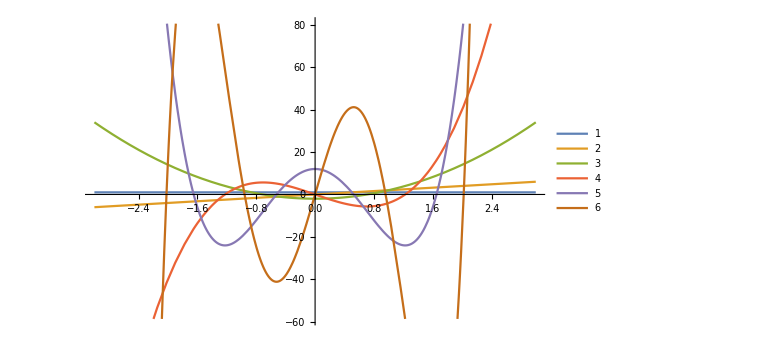

```mathematica
Plot[Table[HermiteH[n,x],{n,0,5}]//Evaluate,
{x,-3,3},PlotLegends->Automatic,ImageSize->Large]
```